```mathematica
2^67
```

147573952589676412928

```mathematica
Times[2,45]
```

90

```mathematica
Divide[256,5]
```

256/5

```mathematica
Divide[25,5]
```

5

```mathematica
2/3
```

2/3

```mathematica
2./3.
```

0.666667

```mathematica
A*B
```

A B

```mathematica
Fibonacci[45]
```

1134903170

```mathematica
ScientificForm[N[1134903170,10]]
```

1.134903170×10^9

```mathematica
NumberForm[1.13490317`10.*^9]
```

1.134903170×10^9

Solve [ { 2 x ^2 + 3 y == 0 , 3 x + 4 y == 0 } , {x , y } ]

WolframAlphaQueryResults

```mathematica
.2/3
```

0.0666667

```mathematica
2./3
```

0.666667

```mathematica
N[%]
```

0.666667

```mathematica
N[%5]
```

0.666667

```mathematica
N[%^(5^□)]
```

```mathematica
0.6666666666666666^(5.^□)
```

```mathematica
Sqrt[4]
```

2

```mathematica
Abs[6.7]
```

6.7

```mathematica
Floor[5.6]
```

5

```mathematica
Ceiling[7.8]
```

8

```mathematica
(*List - collection of data in a list *)
```

## List

```mathematica
m = {{3,4,5},{3,4,3},{6,5,4}}//MatrixForm
```

(3 | 4 | 5
3 | 4 | 3
6 | 5 | 4)

```mathematica
x+ y +4
```

4+x+y

```mathematica
x+ y +4/.{ x -> 3 , y -> 4 }
```

11

## Replacement Operator

```mathematica
f[x_] := x^3 /.{x -> 4}
```

```mathematica
Function[x,x^3/.{x->4}]
```

Function[x,x^3/.{x→4}]

```mathematica
Clear[x]
```

```mathematica
f[x_] := [x^3 ,{x ,2,10}]
```

```mathematica
num = {1 ,2}
```

{1,2}

```mathematica
num
```

{1,2}

```mathematica
objects = { "apple", "repel" , "banana" }
```

{apple,repel,banana}

```mathematica
objects
```

{apple,repel,banana}

```mathematica
2* { 1,2,3,4,56,127}
```

{2,4,6,8,112,254}

## Table Form

```mathematica
Table[ { i^2 ,i^3} , {i,5,15}]// TableForm
```

25 | 125
36 | 216
49 | 343
64 | 512
81 | 729
100 | 1000
121 | 1331
144 | 1728
169 | 2197
196 | 2744
225 | 3375

## Multiplication of matrices m and m2

```mathematica
m  = { { 1,2} , { 3,4 } , {5,6}};
m2 = {{12,23,20},{56,65,87}};
m.m2 //MatrixForm (*dot product of matrices*)
```

```mathematica
({{124, 153, 194}, {260, 329, 408}, {396, 505, 622}})
```

## PLot Graph

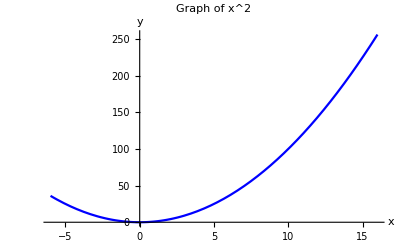

```mathematica
f[x_] := x^2
Plot[x^2 , {x,-6,16},PlotStyle -> Blue , AxesLabel->{"x" , "y"}, PlotLabel-> "Graph of x^2"]
```

## Function

```mathematica
Log[1]
```

0

```mathematica
N[Sin[30]]
```

-0.988032

```mathematica
ArcSin[1]
```

π/2

```mathematica
Exp[56]
```

ⅇ^56

```mathematica
ArcSin[.2]
```

0.201358

```mathematica
With[{d=N[0.2013579207903308/°]},Defer[d °]]
```

11.537 °

```mathematica
Range[5] (* Numbers between 1 to 5*)
```

{1,2,3,4,5}

```mathematica
Range[34,50]//TableForm
```

34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50

```mathematica
Table[{i^2,i^6},{i,6,10}] //TableForm
```

36 | 46656
49 | 117649
64 | 262144
81 | 531441
100 | 1000000

```mathematica
%
```

{{36,46656},{49,117649},{64,262144},{81,531441},{100,1000000}}

```mathematica
N[%]
```

{{36.,46656.},{49.,117649.},{64.,262144.},{81.,531441.},{100.,1.×10^6}}

```mathematica
N[%14]
```

0.666667

```mathematica
N[%7]
```

1.1349×10^9

```mathematica
objects
```

{apple,repel,banana}

```mathematica
Pi
```

π

```mathematica
N[Pi,45]
```

3.1415926535897932384626433832795028841971694